# MATH 263 Numerical differential equations

Ethan Smith

## Lecture 5: Multistep methods 4 MAR 2021

## Method implementations.

Disclaimer: The implementations below are not efficient in Mathematica, but they have been chosen for pedagogical reasons.

```mathematica
euler[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n]},
{x[0],y[0]} =N[ {a,y0}];
Do[
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*f[x[i],y[i]];,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]]
];
```

```mathematica
heun[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n],k1,k2,w1=0.5,w2=0.5},
{x[0],y[0]} = N[{a,y0}];
Do[
k1=f[x[i],y[i]];
k2=f[x[i]+h,y[i]+h*k1];
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*(w1*k1 + w2*k2);,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]]
];
```

```mathematica
rk4[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n], k1, k2, k3, k4, w1=1./6, w2=1./3, w3=1./3,w4=1./6},
{x[0],y[0]} = N[{a,y0}];
Do[
k1=f[x[i],y[i]];
k2=f[x[i]+0.5*h,y[i]+0.5*h*k1];
k3=f[x[i]+0.5*h,y[i]+0.5*h*k2];
k4=f[x[i]+h,y[i]+h*k3];
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*(w1*k1+w2*k2+w3*k3+w4*k4);,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]];
];
```

```mathematica
ab2[f_,a_,b_,y0_,n_]:=Module[{x,y,h=N[(b-a)/n],f1,f2},
{{x[0],y[0]},{x[1],y[1]}}=heun[f,a,a+h,y0,1];
f2=f[x[0],y[0]];
Do[
f1=f[x[i],y[i]]; 
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*(3*f1-f2)/2;
(*Shift f evals down to get ready for next step.  Could be done without actually moving the data, but not worth the effort here.*)
f2=f1;,
{i,1,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]];
];
```

## Multistep methods.

The methods that we have considered so far are all called single-step methods because the point  (x_(i+1),y_(i+1)) is computed using only information from the previous step, namely (x_i,y_i).  In particular, the methods have all depended on a formula of the form

y_(i+1) = y_i + h ϕ(x_i,y_i,h).

These methods are also called starting methods because the initial-value condition y(x_0)=y_0 gives enough information to use these methods from the start.  On the other hand, multistep methods use more than one of the previously computed y_j.  An m-step method would use the previous m values: (x_i,y_i), (x_(i-1),y_(i-1)), ..., (x_(i-m+1),y_(i-m+1)).   Linear multistep methods take the form

y_(i+1) = ∑_(j=1)^m α_j y_(i+1-j) + (h∑)_(j=0)^m β_j f(x_(i+1-j),y_(i+1-j)) .

Clearly such a method cannot be used until m previous values are known.  For this reason, these methods must be paired with a starting method and are themselves called continuing methods.  However, there is additional wrinkle if β_0≠ 0 since in that case y_(i+1) appears on both sides of the equation (2).  If β_0=0, the method is said to be explicit; otherwise, the method is said to be implicit.   If the method is implicit and the function f(x, y) is linear in y, then it is easy to solve for y_(i+1) once the specific IVP is given, but in practice this is often not the case.  We will consider implicit methods next week.  For now, we concentrate on the case of explicit methods.  Some of the most popular explicit linear multistep methods are the Adams–Bashforth methods.

### Adams–Bashforth 2-step (explicit) method.

As usual, consider the first order IVP

y’ = f(x,y), y(x_0)=y_0.

Here we derive the 2-step Adam-Bashforth method, which takes the form

y_(i+1)=α_1 y_i+h(β_1 f(x_i,y_i)+β_2 f(x_(i-1),y_(i-1))).

The idea is to force the formula to be exact for the first 3 terms of the Taylor series for the true solution y.  This will ensure that the local truncation error for the method is O(h^3).  Note that with only 3 parameters to determine (viz, α_1,β_1,β_2), this is the best that can be done.  By linearity, it is enough to make it exact for the cases y(x)=1, y(x)=x, and y(x)=x^2.  If y(x) =1, then f(x,y(x)) = y'(x) = 0 and so (3) becomes

1=α_1.

Similarly, if y(x)=x, then y'(x)=1 and (3) becomes

x_(i+1)=α_1 x_i+h(β_1+β_2).

Finally, if y(x)=x^2, then y'(x)=2x and (3) becomes

x_(i+1)^2=α_1 x_i^2+h(β_1·2 x_i+β_2·2 x_(i-1)).

The equations (4), (5), and (6) must hold for all values of x_i and h.   So, we choose x_(i-1)=0 and h=1 so that x_i=1 and x_(i+1)=2.  Then (4), (5), and (6) simplify to

1=α_1,
2=α_1+β_1+β_2,
4=α_1+2β_1.

Solving the system gives α=1, β_1=3/2, and β_2=-1/2.  Thus, the Adams-Bashforth two-step (explicit) method is defined by the recurrence

y_(i+1)=y_i+h/2(3 y'_i-y'_(i-1)),

where y'_i = f(x_i,y_i) for each i≥1.  As we noted above, the local truncation error for the method is O(h^3).  This makes it an order 2 method.  Thus, it should be paired with a starter method whose order of accuracy is at least 2.  In the implementation section, we paired it with Heun’s method.

### Adams–Bashforth 4-step (explicit) method.

In a similar manner, one may derive the Adams–Bashforth four-step (explicit) method, which is defined by the recurrence

y_(i+1)=y_i+h/24(55 y'_i-59 y'_(i-1)+37 y'_(i-2)-9 y'_(i-3))

and has local truncation error that is O(h^5).  Thus, it should be paired with an order 4 starting method such as the classical RK4 method.

### Advantages and disadvantages.

The disadvantage of a multistep method is that it is typically slightly more difficult to implement than a single-step method.  It even requires a single-step method to get started.  However, there tends to be a major gain in order of accuracy per work.  We usually measure the work per step of a numerical method based on the number of times that we need to evaluate the “right-hand side” function f(x,y).  The typical single-step Runge-Kutta method of order 2 (e.g., Heun’s method) requires 2 functional evaluations per step.  We compare this to the Adams–Bashforth 2-step method which has the same order of accuracy and only requires one additional functional evaluation per step since it saves the evaluations from previous steps until it is finished with them.   Furthermore, since the error |y(x_i)-y_i| tends to increase with i, it is reasonable to hope a multistep may have better accuracy (not just order of accuracy) by mere fact that it explicitly incorporates more accurate previous data when approximating y_(i+1).

## Example.

Consider the IVP y'=y-x^2+1, y(0)=1/2.

```mathematica
f[x_,y_]=y-x^2+1;
{x0,y0}={0,1/2};
Y[x_]=y[x]/.DSolve[{y'[x]==f[x,y[x]],y[x0]==y0},y[x],x][[1]];
StringForm["The exact solution to the IVP is ``.",TraditionalForm[y[x]==Y[x]]]
```

The exact solution to the IVP is y(x)==1/2 (2 x^2+4 x-ⅇ^x+2).

Compare Heun’s method and the Adams–Bashforth 2-step method (AB2) with n=10 steps over the interval [a,b]=[0,2].

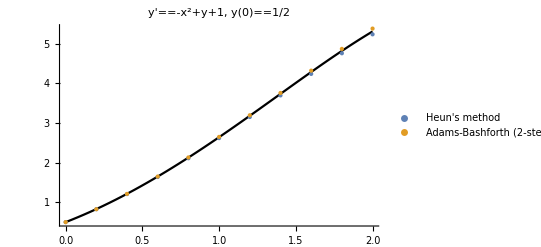

i | Heun | AB2
0 | 0. | 0.
1 | 0.00329862 | 0.00329862
2 | 0.00716765 | 0.00228765
3 | 0.0116982 | 0.0002006
4 | 0.0169938 | 0.00295246
5 | 0.0231715 | 0.00750351
6 | 0.0303627 | 0.0139116
7 | 0.0387138 | 0.0227729
8 | 0.0483866 | 0.0348556
9 | 0.0595577 | 0.0511477
10 | 0.0724173 | 0.0729153|y(x_i)-y_i|

```mathematica
{a,b}={0,2};
n=10;

(*Solve with each method.*)
ab2Soln=ab2[f,a,b,y0,n];
heunSoln=heun[f,a,b,y0,n];

(*Compare with plots.*)
Show[
Plot[Y[x],{x,a,b},PlotStyle->Black],
ListPlot[{heunSoln,ab2Soln},PlotStyle->PointSize[Large],PlotLegends->{"Heun's method","Adams-Bashforth (2-step) method"}],
PlotRange->All,
PlotLabel->StringForm["``, ``",TraditionalForm[y'==f[x,y]],TraditionalForm[y[x0]==y0]]
]

(*Compare absolute errors at each step with a table.*)
h=N[(b-a)/n];
exactSoln=Table[Y[a+h*i],{i,0,n}];
heunSoln=heunSoln[[;;,2]];
heunErrors=Abs[heunSoln-exactSoln];
ab2Soln=ab2Soln[[;;,2]];
ab2Errors=Abs[ab2Soln-exactSoln];
Labeled[TableForm[Table[{i-1,heunErrors[[i]],ab2Errors[[i]]},{i,1,n+1}],TableHeadings->{None,{"i","Heun","AB2"}}],"|y(x_i)-y_i|",Top]
```

Use both Heun’s method and AB2 to approximate y(2) with n=10^j steps for j=1,...,6.  Compare the absolute errors and the time to compute each result.

```mathematica
numSteps=Table[10^j,{j,1,6}];
```

```mathematica
(*Compute absolute errors and display in table.*)
ynHeun = Table[Last[heun[f,a,b,y0,n]][[2]],{n,numSteps}];
ynAB2 = Table[Last[ab2[f,a,b,y0,n]][[2]],{n,numSteps}];
heunErrors=Abs[ynHeun-Y[b]];
ab2Errors=Abs[ynAB2-Y[b]];
Labeled[TableForm[Transpose[Join[{numSteps,heunErrors,ab2Errors}]],TableHeadings->{None,{"n","Heun","AB2"}}],StringForm["|``-y_n|",TraditionalForm[y[b]]],Top]
```

n | Heun | AB2
10 | 0.0724173 | 0.0729153
100 | 0.000779726 | 0.00117961
1000 | 7.84668×10^-6 | 0.0000122633
10000 | 7.85146×10^-8 | 1.231×10^-7
100000 | 7.79417×10^-10 | 1.23723×10^-9
1000000 | 4.34142×10^-12 | 2.43991×10^-11|y(2)-y_n|

```mathematica
(*Recompute to get times.  It is wasteful to compute the solution twice, but the code is easier to read.*)
heunTimes=Table[Timing[heun[f,a,b,y0,n];][[1]],{n,numSteps}];
ab2Times=Table[Timing[ab2[f,a,b,y0,n];][[1]],{n,numSteps}];
Labeled[TableForm[Join[{numSteps,heunTimes,ab2Times}],TableHeadings->{{"n","Heun", "AB2"},None}],"Running times (seconds)",Top]
```

n | 10 | 100 | 1000 | 10000 | 100000 | 1000000
Heun | 0.000232 | 0.001299 | 0.011343 | 0.103122 | 1.05123 | 11.7129
AB2 | 0.000225 | 0.000968 | 0.008439 | 0.077146 | 0.830743 | 10.1528Running times (seconds)